## Initialization

```mathematica
(* Switch to the directory the notebook and data files are in *)
SetDirectory[NotebookDirectory[]]
```

/Users/npadmana/myWork/np_sandbox/diff_transfer_fn

```mathematica
(* Number of files *)
```

```mathematica
nfiles = 5;
```

```mathematica
(* Set the file name list *)
```

```mathematica
fnames = "test_transfer_z"<>ToString[#]<>".dat"& /@ Range[0,nfiles-1];
```

```mathematica
(* Read in all the files *)
```

```mathematica
transfers = Import[#, "Table"] & /@ fnames;
```

```mathematica
Dimensions[transfers]
```

{5,692,7}

```mathematica
tb0 = t0[[All, {1,3}]];
```

```mathematica
tb4 = t4[[All, {1,3}]];
```

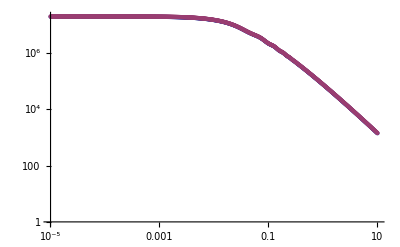

```mathematica
ListLogLogPlot[{tb0,tb4}]
```

```mathematica
dtb = tb4[[All, 2]]/tb4[[1,2]] - tb0[[All, 2]]/tb0[[1,2]];
```

```mathematica
k = tb0[[All, 1]];
```

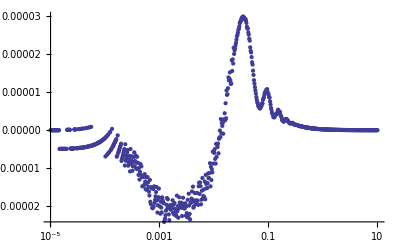

```mathematica
ListLogLinearPlot[Thread[{k, dtb}]]
```